#### Author and License Information Author : Zoey Zhiyuan Dong Date : 2024 - 12 - 11 License : This code is shared under the MIT License for academic and research purposes.

Preparation
This notebook demonstrates the fitting process for obtaining anisotropy model parameters based on given inputs: transition pressure, density gap, fluid sound speed. The code presented here is based on the methods described in [Paper link]. Here, we will load and process a complete example dataset for hybrid star model with: transition pressure=2e33 dyn cm^-2,  density gap=1e14 g cm^-3, fluid sound speed=0.33.

#### Step1: Fit σ with Eq.(29) The input files are organized within a main folder, which contains several subfolders named after different values of \bar{κ}. Each sub-folder contains a series of text files named by central pressure values (in km^-2). The contents of each text file are as follows: • radius(data[[All, 1]]): radius (km), indicating the radial distance from the center to the surface of the star. • sigmaoverpc (data[[All, 2]]): Normalized anisotropy parameter , obtained through numerical solution. • Pr (data[[All, 3]]): Radial pressure (km^-2), describing the radial pressure distribution as a function of radius. • mass (data[[All, 4]]): Mass component (Caution! It is NOT in units of solar Mass=1.4767291 km!). • rhooverrhoc (data[[All, 5]]): Normalized density component , where rhoc represents the central density. • zvalues (data[[All, 6]]): a dimensionless ratio that quantifies the degree of anisotropy in the material. Each output file is stored in the ‘sigmafit’ folder within the main directory. File names correspond to the shear value (\bar{κ}). Each output .txt file contains rows of data in the order: • central pressure(km^-2) • \bar{κ} • estimatedLambda(λ) • estimatedn: this index is different from the one we use in Eq.(29), we use n here, and the relation between n and N is: n=N/λ-1

```mathematica
ClearAll["Global`*"]
(*Read files*)
baseFolderPath="/Users/zhiyuandong/Desktop/main folder";
pcFolders=Select[FileNames["*",baseFolderPath],DirectoryQ[#]&&Not[StringContainsQ[#,{".DS_Store","Readme.rtf","sigmafit"}]]&];
results={};

Do[folderPath=pcFolder;
files=FileNames["*.txt",folderPath];

Do[Print[file];
data=Import[file,"Table","FieldSeparators"->" "];
If[MatrixQ[data,NumericQ],radius=data[[All,1]];
sigmaoverpc=data[[All,2]];
Pr=data[[All,3]];
mass=data[[All,4]];
rhooverrhoc=data[[All,5]];
zvalues=data[[All,6]];
(*Nonlinear fitting for Eq.(29)*)
fit=NonlinearModelFit[Transpose[{radius,mass,rhooverrhoc,sigmaoverpc}],Lambda m rho^n/(r (1-2 m/r)),{Lambda,n},{r,m,rho}];
estimatedLambda=Lambda/. fit["BestFitParameters"];
estimatedN=n/. fit["BestFitParameters"];
Print["lambda = ",estimatedLambda];
Print["n = ",estimatedN];
(*error*)
fitValue=estimatedLambda *mass* rhooverrhoc^estimatedN/(radius (1-2 mass/radius));
error=(fitValue-sigmaoverpc)/sigmaoverpc;

(*output*)
pcValue=StringReplace[FileNameTake[file],{"pcenter_"->"",".txt"->""}];
numericalPart=StringSplit[pcFolder,"/"]//Last;
shearValue=numericalPart;
AppendTo[results,{pcValue,shearValue,estimatedLambda,estimatedN}];,(*Else*)Print["Invalid data in file: ",file]],{file,files}];
Export[FileNameJoin[{baseFolderPath,"sigmafit",numericalPart<>".txt"}],results,"Table"];
results={};  (*Clear results for next pc folder iteration*),{pcFolder,pcFolders}]
```

#### Step 2: fit λ and n (N) with Eq.(30) Input: sigmafit.txt Output file: kappafit.txt. Each line in this file contains the following values: • fileBaseName: the value of \bar{κ} (Estimated paramters for -λ) • estimateda: a1 • estimatedb: a2 • estimatedc: a3 • estimatedd: a4 • estimatede: a0 (Estimated paramters for -N) • estimatedk: a1 • estimateds: a2 • estimatedl: a3 • estimatedj: a4 • estimatedh: a0

```mathematica
ClearAll["Global`*"];
(*read files*)
pcFiles1=Select[FileNames["*","/Users/zhiyuandong/Desktop/main folder/sigmafit"],Not[StringContainsQ[#,".DS_Store"]]&];
readData[file_]:=Import[file,"Table"];

fitAndPlotError[pcFile_]:=Module[{pcData,transposedData,pc1,kappa1,lambda1,n1,n1Incremented,fitLambda,fitN,estimateda,estimatedb,estimatedc,estimatedd,estimatede,estimatedk,estimateds,estimatedl,estimatedj,estimatedh,lambdaFitFunc,bothFunc,Rerrorlambda,Rerrorboth,fitErrorPlotlambda,fitErrorPlotboth,outputData,fileName,fileBaseName},pcData=readData[pcFile];
Print[pcFile];
(*read data*)
transposedData=Transpose[pcData];
pc1=transposedData[[1]];
kappa1=transposedData[[2]];
lambda1=transposedData[[3]];
n1=transposedData[[4]];
n1Incremented=Map[#+1&,n1];
(*fitting*)
fitLambda=NonlinearModelFit[Transpose[{pc1,Log[-lambda1]}],a*Log[Pc]+b*Log[Pc]^2+c*Log[Pc]^3+d*Log[Pc]^4+e,{a,b,c,d,e},Pc];
fitN=NonlinearModelFit[Transpose[{pc1,Log[-n1Incremented*lambda1]}],k*Log[Pc]+s*Log[Pc]^2+l*Log[Pc]^3+j*Log[Pc]^4+h,{k,s,l,j,h},Pc];
fileBaseName=StringReplace[FileNameTake[pcFile],{".txt"->""}];
{estimateda,estimatedb,estimatedc,estimatedd,estimatede}=Values[fitLambda["BestFitParameters"]];
{estimatedk,estimateds,estimatedl,estimatedj,estimatedh}=Values[fitN["BestFitParameters"]];
Print["Fit Parameters for lambda: ",{estimateda,estimatedb,estimatedc,estimatedd,estimatede}];
Print["Fit Parameters for n*lambda: ",{estimatedk,estimateds,estimatedl,estimatedj,estimatedh}];
(*output*)
outputData={fileBaseName,estimateda,estimatedb,estimatedc,estimatedd,estimatede,estimatedk,estimateds,estimatedl,estimatedj,estimatedh};
fileName="/Users/zhiyuandong/Desktop/main folder/kappafit.txt";
If[Not[FileExistsQ[fileName]],stream=OpenWrite[fileName];
WriteString[stream,StringJoin[Riffle[Map[ToString,outputData],"\t"],"\n"]];
Close[stream];,stream=OpenAppend[fileName];
WriteString[stream,"\n"];WriteString[stream,StringJoin[Riffle[Map[ToString,outputData],"\t"],"\n"]];Close[stream];];
(*error*)
lambdaFitFunc=estimateda*Log[pc1]+estimatedb*Log[pc1]^2+estimatedc*Log[pc1]^3+estimatedd*Log[pc1]^4+estimatede;
bothFunc=estimatedk*Log[pc1]+estimateds*Log[pc1]^2+estimatedl*Log[pc1]^3+estimatedj*Log[pc1]^4+estimatedh;
Rerrorlambda=Abs[(-Exp[lambdaFitFunc]-lambda1)/lambda1];
Rerrorboth=Abs[(-Exp[bothFunc]-n1Incremented*lambda1)/(n1Incremented*lambda1)];
fitErrorPlotlambda=ListLogPlot[Transpose[{pc1,Rerrorlambda}],PlotStyle->Red,PlotLegends->{"Fitted error lambda"}];
fitErrorPlotboth=ListLogPlot[Transpose[{pc1,Rerrorboth}],PlotStyle->Blue,PlotLegends->{"Fitted error n*lambda^2"}];
Print[Show[fitErrorPlotlambda,Frame->True,FrameLabel->{"pc","Relative error lambda"},PlotRange->All,ImageSize->Large]];
Print[Show[fitErrorPlotboth,Frame->True,FrameLabel->{"pc","Relative error n*lambda^2"},PlotRange->All,ImageSize->Large]];];

Do[fitAndPlotError[file],{file,pcFiles1}];
fileName="/Users/zhiyuandong/Desktop/main folder/kappafit.txt";
If[FileExistsQ[fileName],data=DeleteCases[Import[fileName,"Lines"],""];
Export[fileName,data,"Lines"];];
```

## Step 3: generate bi and c1, c2, c3, c4 with Eq.(31) Input: kappafit.txt Output file: paramters.txt The file contains a 10-row by 9-column dataset. We put this results in Table I and II in our paper. • The first 5 rows correspond to the parameters for -λ and are arranged in the order of a0, a1, a2, a3, and a4. • The last 5 rows correspond to the parameters for -N, following the same a0 through a4 sequence. Each of the 9 columns represents a specific parameter in the order: b0, b1, b2, b3, b4, c1, c2, c3, c4.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 2000 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{{b0→21.298,b1→-2.49236,b2→-0.0441158,b3→0.0214416,b4→-0.000953724,c1→-0.000287918,c2→-22.5193,c3→-5.19451,c4→6.40381},{b0→4.04999,b1→-0.464404,b2→-0.0025245,b3→0.00317659,b4→-0.000143405,c1→-0.0000675698,c2→-4.39753,c3→-5.90323,c4→6.79181},{b0→0.383589,b1→-0.0439679,b2→0.00028338,b3→0.000215801,b4→-9.83734×10^-6,c1→-6.38893×10^-6,c2→-0.474466,c3→-7.23002,c4→7.55147},{b0→0.0101121,b1→-0.00115794,b2→0.0000207032,b3→4.23028×10^-6,b4→-2.09805×10^-7,c1→-2.13328×10^-7,c2→-0.0129561,c3→-8.17354,c4→7.88381},{b0→-12.7021,b1→8.39923,b2→-1.86551,b3→0.184166,b4→-0.00696914,c1→-0.180117,c2→48.9846,c3→-4.84629,c4→3.14237},{b0→5.17249,b1→-1.45631,b2→0.219247,b3→-0.0190917,b4→0.000707375,c1→-0.000286773,c2→-9.30673,c3→-7.24457,c4→3.73747},{b0→1.23417,b1→-0.3862,b2→0.0631105,b3→-0.00545453,b4→0.00019528,c1→-0.0000918,c2→-4.12719,c3→-8.46605,c4→4.19922},{b0→0.0465864,b1→-0.00877228,b2→0.000868633,b3→-0.0000514987,b4→1.55742×10^-6,c1→0.000160447,c2→-0.000234488,c3→0.249335,c4→0.143133},{b0→0.00629663,b1→-0.000994696,b2→0.00007815,b3→-3.83765×10^-6,b4→1.04743×10^-7,c1→9.53574×10^-7,c2→-1.23109,c3→-74.2622,c4→-22.4138},{b0→-18.9117,b1→9.59313,b2→-2.03843,b3→0.191224,b4→-0.00686983,c1→-0.179742,c2→71.6922,c3→-5.58423,c4→3.45408}}

General::munfl: -0.000234488 1.37179×10^-307 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-743.825] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-779.268] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

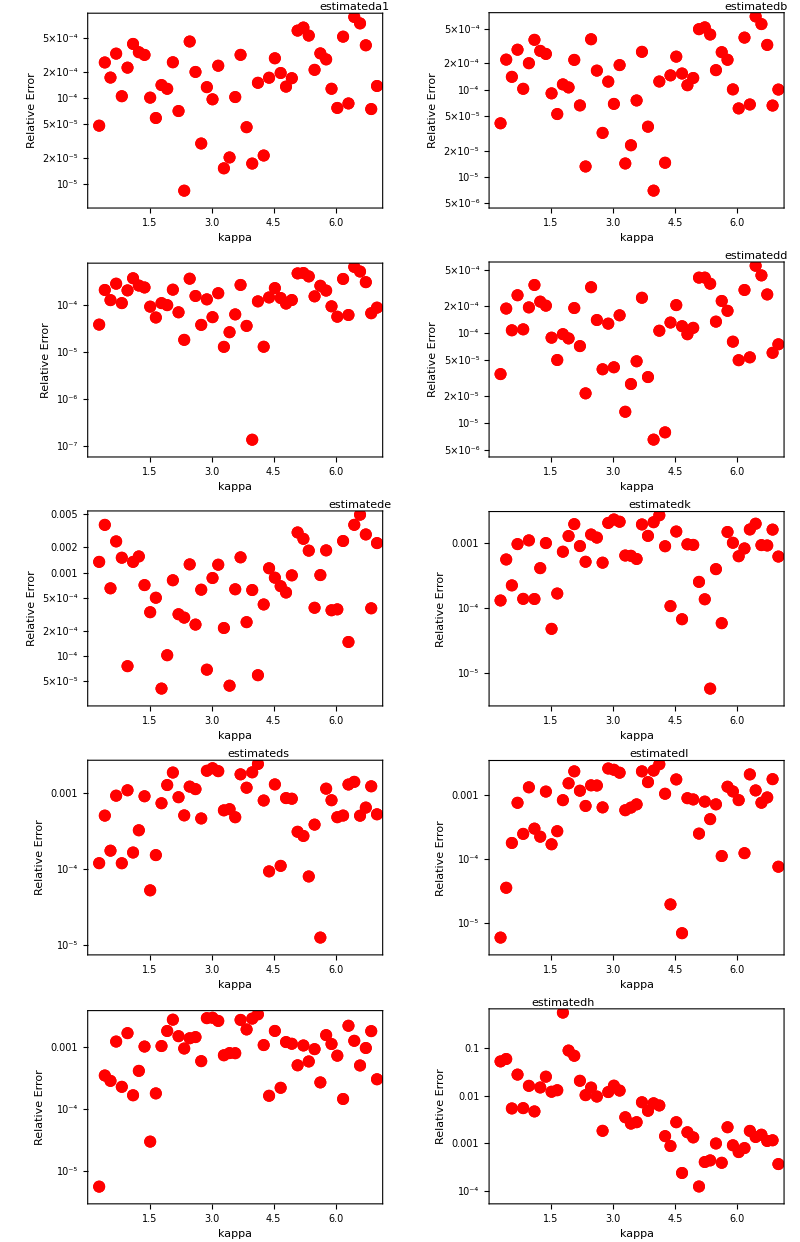

```mathematica
ClearAll["Global`*"];
(*read data*)
fileName="/Users/zhiyuandong/Desktop/main folder/kappafit.txt";
data=Import[fileName,"Table"];
fileBaseNames=data[[All,1]];
parameters=data[[All,{2,3,4,5,6,7,8,9,10,11}]];  
parameterNames={"estimateda1","estimatedb","estimatedc","estimatedd","estimatede","estimatedk","estimateds","estimatedl","estimatedj","estimatedh"};
(*fitting*)
fits=Table[NonlinearModelFit[Transpose[{fileBaseNames,parameters[[All,i]]}],c2 Exp[-((kappa-c3)^2/(2c4^2))]+b1*kappa+b2*kappa^2+b3*kappa^3+b4*kappa^4+b0+c1/kappa,{b0,b1,b2,b3,b4,c1,c2,c3,c4},kappa,MaxIterations->2000],{i,Length[parameters[[1]]]}];
fitCoefficients=Table[fits[[i]]["BestFitParameters"],{i,Length[fits]}];
Print[fitCoefficients];
coefficientsValues=Table[Values[fitCoefficients[[i]]],{i,Length[fitCoefficients]}];
(*error*)
fitFunctions=Table[c2 Exp[-((kappa-c3)^2/(2c4^2))]+b1*kappa+b2*kappa^2+b3*kappa^3+b4*kappa^4+b0+c1/kappa/. fitCoefficients[[i]],{i,Length[fitCoefficients]}];
relativeErrors=Table[With[{fitFunc=fitFunctions[[i]]},Abs[(fitFunc/. kappa->#&/@fileBaseNames-parameters[[All,i]])/parameters[[All,i]]]],{i,Length[parameters[[1]]]}];
relativeErrorPlots=Table[ListLogPlot[Transpose[{fileBaseNames,relativeErrors[[i]]}],PlotRange->All,PlotLabels->Placed[parameterNames[[i]],Above],Frame->True,FrameLabel->{"kappa","Relative Error"},ImageSize->Large,Joined->False,PlotStyle->{Red,PointSize[0.015]} ],{i,Length[relativeErrors]}];
GraphicsGrid[Partition[relativeErrorPlots,2],Spacings->{4,4}]
(*output*)
coefficientsFileName="/Users/zhiyuandong/Desktop/main folder/parameters.txt";
Export[coefficientsFileName,coefficientsValues,"Table"];
```